```mathematica
DSolve[-ρ D[(ρ ψ'[ρ]), ρ]==μ^2 ψ[ρ],ψ[ρ],ρ]//FullSimplify
```

{{ψ[ρ]→C[1] Cos[μ Log[ρ]]+C[2] Sin[μ Log[ρ]]}}

```mathematica
FullSimplify[Series[(√(2μ Sinh[π μ]))/π BesselK[ⅈ μ,m ρ],{m,0,1}],Assumptions->m>0&&ρ>0]
```

m^(ⅈ μ) ((2^(-1/2-ⅈ μ) ρ^(ⅈ μ) Gamma[-ⅈ μ] √(μ Sinh[π μ]))/π+O[m]^2)+m^(-ⅈ μ) ((2^(-1/2+ⅈ μ) ρ^(-ⅈ μ) Gamma[ⅈ μ] √(μ Sinh[π μ]))/π+O[m]^2)

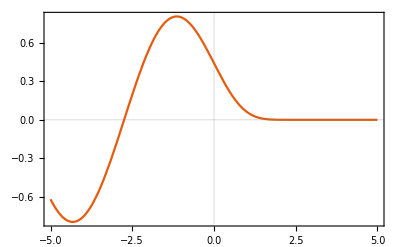
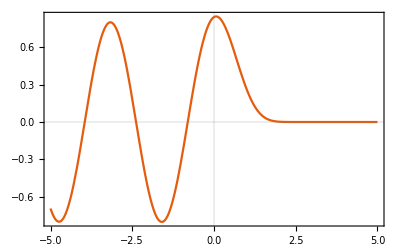
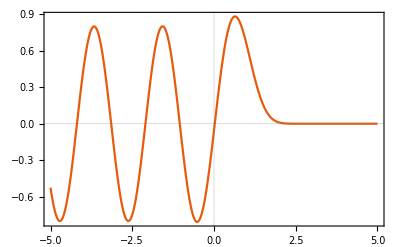
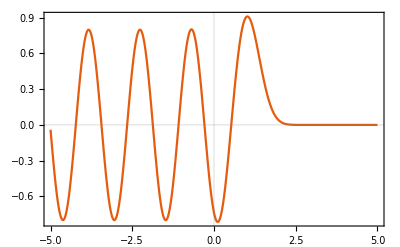
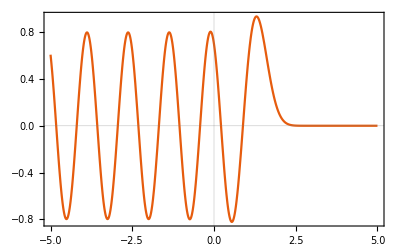
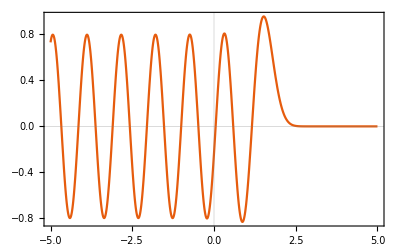
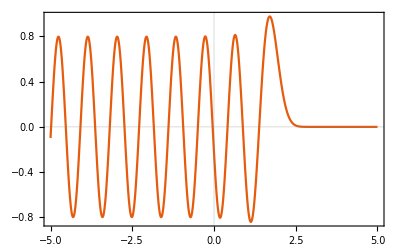
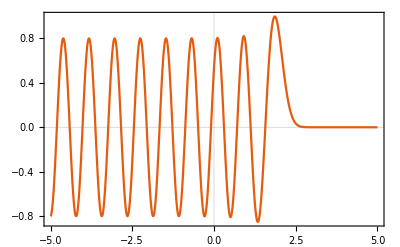

-Graphics-

```mathematica
Table[Plot[Re@((√(2μ Sinh[π μ]))/π)BesselK[ⅈ μ,ⅇ^z],{z,-5,5},PlotTheme->"Scientific"],{μ,10}]
ContourPlot[Re@((√(2μ Sinh[π μ]))/π)BesselK[ⅈ μ,ⅇ^z],{z,-5,5},{μ,-5,5},PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
{ⅈ(x D[Ψ[x,t], t]+t D[Ψ[x,t], x])==κ/a Ψ[x,t],D[Ψ[x,t], t,t]-D[Ψ[x,t], x,x]==0}
FullSimplify[%,Assumptions->t∈Reals&&x∈Reals]
FullSimplify[DSolve[%[[2]],Ψ,{x,t}],Assumptions->t∈Reals&&x∈Reals]
FullSimplify[%%[[1]]/.%[[1]],Assumptions->t∈Reals&&x∈Reals]
FullSimplify[%/.{t->(v+u)/2,x->(v-u)/2},Assumptions->u∈Reals&&v∈Reals]
{%/.C[2]->(0&),%/.C[1]->(0#&)}
MapThread[DSolve[%[[#1]],C[#1],#2]&,{{1,2},{u,v}}]//Flatten
{C[1][u],C[2][v]}/.%;
FullSimplify[{%[[1]]/.C[2]->(-u0)^(-ⅈ κ/a),%[[2]]/.C[3]->v0^(ⅈ κ/a)},Assumptions->u0>0&&v0>0&&u<0]
%/.{u->t-x,v->t+x}/.{t->0,x->1/a}
```

{ⅈ (x Ψ^(0,1)[x,t]+t Ψ^(1,0)[x,t])==(κ Ψ[x,t])/a,Ψ^(0,2)[x,t]-Ψ^(2,0)[x,t]==0}

{(ⅈ κ Ψ[x,t])/a+x Ψ^(0,1)[x,t]+t Ψ^(1,0)[x,t]==0,Ψ^(0,2)[x,t]==Ψ^(2,0)[x,t]}

{{Ψ→Function[{x,t},C[1][t-x]+C[2][t+x]]}}

(ⅈ κ (C[1][t-x]+C[2][t+x])+a (-t+x) C[1]'[t-x]+a (t+x) C[2]'[t+x])/a==0

(ⅈ κ (C[1][u]+C[2][v])-a u C[1]'[u]+a v C[2]'[v])/a==0

{(ⅈ κ C[1][u]-a u C[1]'[u])/a==0,(ⅈ κ C[2][v]+a v C[2]'[v])/a==0}

{C[1]→Function[{u},u^((ⅈ κ)/a) C[2]],C[2]→Function[{v},v^(-(ⅈ κ)/a) C[3]]}

{(-u0/u)^(-(ⅈ κ)/a),(v/v0)^(-(ⅈ κ)/a)}

{(a u0)^(-(ⅈ κ)/a),(1/(a v0))^(-(ⅈ κ)/a)}

```mathematica
FullSimplify[{(ⅈ D[((-t+x)/u0)^(ⅈ κ), t])/((-t+x)/u0)^(ⅈ κ),(ⅈ D[((t+x)/v0)^(-ⅈ κ), t])/((t+x)/v0)^(-ⅈ κ)},Assumptions->t-x<0&&t+x>0&&u0>0&&v0>0]
FullSimplify[{(ⅈ D[((t-x)/u0)^(ⅈ κ), t])/((t-x)/u0)^(ⅈ κ),(ⅈ D[((-t-x)/v0)^(-ⅈ κ), t])/((-t-x)/v0)^(-ⅈ κ)},Assumptions->t-x>0&&t+x<0&&u0>0&&v0>0]
{(ⅈ D[((-t+x)/u0)^(-ⅈ κ), t])/((-t+x)/u0)^(-ⅈ κ),(ⅈ D[((t+x)/v0)^(ⅈ κ), t])/((t+x)/v0)^(ⅈ κ)}//FullSimplify
```

{κ/(-t+x),κ/(t+x)}

{-κ/(t-x),κ/(t+x)}

{κ/(t-x),-κ/(t+x)}

```mathematica
ⅈ(#1 D[#2, t]-(D[#1, t])#2)&;
FullSimplify[%[((t-x)/-u0)^(-ⅈ κ1/a),((t-x)/-u0)^(ⅈ κ2/a)],Assumptions->x>t&&κ1>0&&κ2>0]
%%[((t+x)/v0)^(ⅈ κ1/a),((t+x)/v0)^(-ⅈ κ2/a)]//FullSimplify
FullSimplify[%%%[((t-x)/u0)^(-ⅈ κ1/a),((t-x)/u0)^(ⅈ κ2/a)],Assumptions->x<t]
```

(((-t+x)/u0)^(-(ⅈ (κ1-κ2))/a) (-κ1-κ2))/(a (t-x))

(((t+x)/v0)^((ⅈ (κ1-κ2))/a) (κ1+κ2))/(a (t+x))

(((t-x)/u0)^(-1-(ⅈ (κ1-κ2))/a) (-κ1-κ2))/(a u0)

```mathematica
Ψm[κ_,t_,x_]:=1/(√(2π))1/(√(2κ))1/(√(2Sinh[(π κ)/a]))ⅇ^(-Sign[t-x](π κ)/(2a))(Abs[t-x]/u0)^(ⅈ κ/a)
Ψp[κ_,t_,x_]:=1/(√(2π))1/(√(2κ))1/(√(2Sinh[(π κ)/a]))ⅇ^(-Sign[t+x](π κ)/(2a))(Abs[t+x]/v0)^(-ⅈ κ/a)
```

Power::indet: Indeterminate expression 0.^ⅈ encountered.

ContourPlot::exclul: {(x-y) (x+y)-0} must be a list of equalities or real-valued functions.

Power::indet: Indeterminate expression 0.^ⅈ encountered.

ContourPlot::exclul: {(x-y) (x+y)-0} must be a list of equalities or real-valued functions.

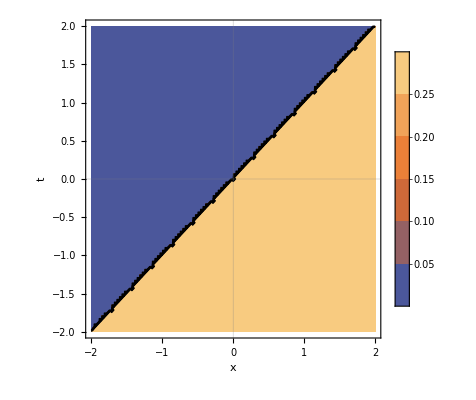
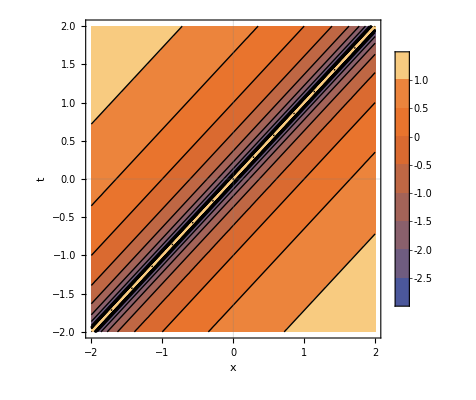

ContourPlot::exclul: {(x-y) (x+y)-0} must be a list of equalities or real-valued functions.

Power::indet: Indeterminate expression 0.^-ⅈ encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

ContourPlot::exclul: {(x-y) (x+y)-0} must be a list of equalities or real-valued functions.

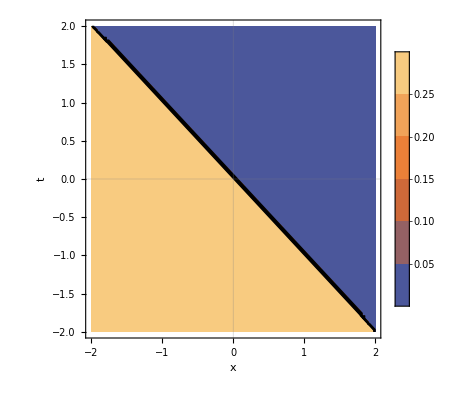
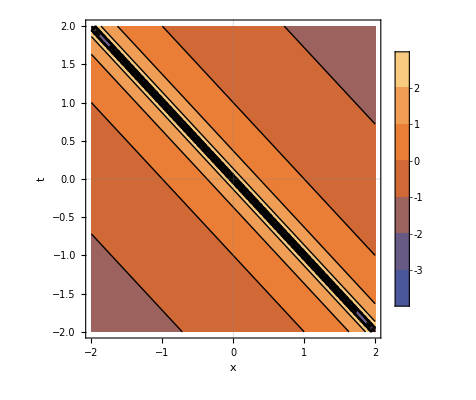

```mathematica
ContourPlot[#[Ψm[1,t,x]/.{a->1,u0->1}],{x,-2,2},{t,-2,2},PlotTheme->"Scientific",Exclusions->(x-y)(x+y)==0,PlotLegends->Automatic,FrameLabel->Automatic]&/@{Abs,Arg}

ContourPlot[#[Ψp[1,t,x]/.{a->1,v0->1}],{x,-2,2},{t,-2,2},PlotTheme->"Scientific",Exclusions->(x-y)(x+y)==0,PlotLegends->Automatic,FrameLabel->Automatic]&/@{Abs,Arg}
```

```mathematica
1-Tanh[x]^2//TrigToExp//Simplify//ExpToTrig//Simplify
```

Sech[x]^2

Piecewise[{{(ⅇ^((π κ)/(2 a)-(ⅈ κ Log[(t+x)/(-t+x)])/(2 a)) BesselK[(ⅈ κ)/a,m √((-t+x) (t+x))])/(√2 π), t-x<0&&t+x>0}, {-(ⅈ ⅇ^((π κ)/(2 a)-(ⅈ κ Log[(t+x)/(t-x)])/(2 a)) HankelH2[(ⅈ κ)/a,m √((t-x) (t+x))])/(2 √2), t-x>0&&t+x>0}, {(ⅇ^(-(π κ)/(2 a)-(ⅈ κ Log[-(t+x)/(t-x)])/(2 a)) BesselK[(ⅈ κ)/a,m √((-t+x) (t+x))])/(√2 π), t-x>0&&t+x<0}, {(ⅈ ⅇ^(-(π κ)/(2 a)-(ⅈ κ Log[-(t+x)/(-t+x)])/(2 a)) HankelH1[(ⅈ κ)/a,m √((t-x) (t+x))])/(2 √2), t-x<0&&t+x<0}, {0, True}}]

Piecewise[{{(ⅇ^(π/2) ((t+x)/(-t+x))^(-ⅈ/2) BesselK[ⅈ,√((-t+x) (t+x))])/(√2 π), t-x<0&&t+x>0}, {-(ⅈ ⅇ^(π/2) ((t+x)/(t-x))^(-ⅈ/2) HankelH2[ⅈ,√((t-x) (t+x))])/(2 √2), t-x>0&&t+x>0}, {(ⅇ^(-π/2) (-(t+x)/(t-x))^(-ⅈ/2) BesselK[ⅈ,√((-t+x) (t+x))])/(√2 π), t-x>0&&t+x<0}, {(ⅈ ⅇ^(-π/2) (-(t+x)/(-t+x))^(-ⅈ/2) HankelH1[ⅈ,√((t-x) (t+x))])/(2 √2), t-x<0&&t+x<0}, {0, True}}]

Piecewise[{{1/(2 π √Sinh[(π κ)/a])ⅇ^(-(π κ)/a) ((t+x)/(-t+x))^(-(ⅈ κ)/(2 a)) (-((t+x)/(-t+x))^((ⅈ κ)/a) BesselK[-(ⅈ κ)/a,m √(-t^2+x^2)]+ⅇ^((2 π κ)/a) BesselK[(ⅈ κ)/a,m √(-t^2+x^2)]), t<x&&t+x>0}, {1/(4 √Sinh[(π κ)/a])ⅈ ⅇ^(-(π κ)/a) ((t+x)/(t-x))^(-(ⅈ κ)/(2 a)) (((t+x)/(t-x))^((ⅈ κ)/a) HankelH2[-(ⅈ κ)/a,m √(t^2-x^2)]-ⅇ^((2 π κ)/a) HankelH2[(ⅈ κ)/a,m √(t^2-x^2)]), t>x&&t+x>0}, {((-(t+x)/(t-x))^(-(ⅈ κ)/(2 a)) (-(-(t+x)/(t-x))^((ⅈ κ)/a) BesselK[-(ⅈ κ)/a,m √(-t^2+x^2)]+BesselK[(ⅈ κ)/a,m √(-t^2+x^2)]))/(2 π √Sinh[(π κ)/a]), t>x&&t+x<0}, {-(ⅈ ((t+x)/(t-x))^(-(ⅈ κ)/(2 a)) (((t+x)/(t-x))^((ⅈ κ)/a) HankelH1[-(ⅈ κ)/a,m √(t^2-x^2)]-HankelH1[(ⅈ κ)/a,m √(t^2-x^2)]))/(4 √Sinh[(π κ)/a]), t<x&&t+x<0}, {0, True}}]

Piecewise[{{(ⅇ^-π ((t+x)/(-t+x))^(-ⅈ/2) (-((t+x)/(-t+x))^ⅈ BesselK[-ⅈ,√(-t^2+x^2)]+ⅇ^(2 π) BesselK[ⅈ,√(-t^2+x^2)]))/(2 π √Sinh[π]), t<x&&t+x>0}, {(ⅈ ⅇ^-π ((t+x)/(t-x))^(-ⅈ/2) (((t+x)/(t-x))^ⅈ HankelH2[-ⅈ,√(t^2-x^2)]-ⅇ^(2 π) HankelH2[ⅈ,√(t^2-x^2)]))/(4 √Sinh[π]), t>x&&t+x>0}, {((-(t+x)/(t-x))^(-ⅈ/2) (-(-(t+x)/(t-x))^ⅈ BesselK[-ⅈ,√(-t^2+x^2)]+BesselK[ⅈ,√(-t^2+x^2)]))/(2 π √Sinh[π]), t>x&&t+x<0}, {-(ⅈ ((t+x)/(t-x))^(-ⅈ/2) (((t+x)/(t-x))^ⅈ HankelH1[-ⅈ,√(t^2-x^2)]-HankelH1[ⅈ,√(t^2-x^2)]))/(4 √Sinh[π]), t<x&&t+x<0}, {0, True}}]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

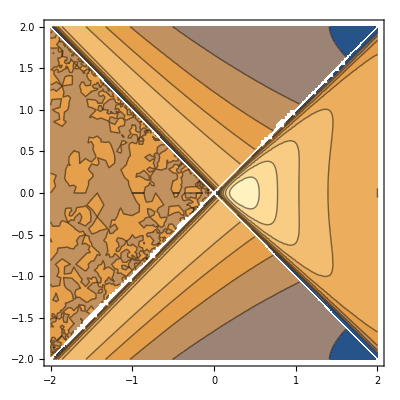
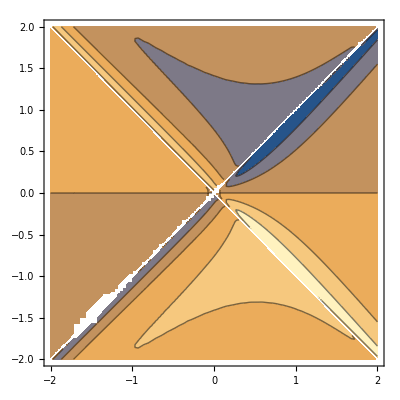

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

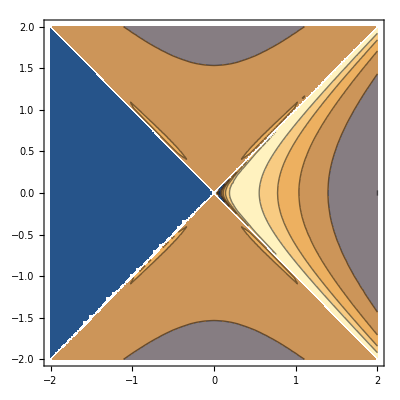
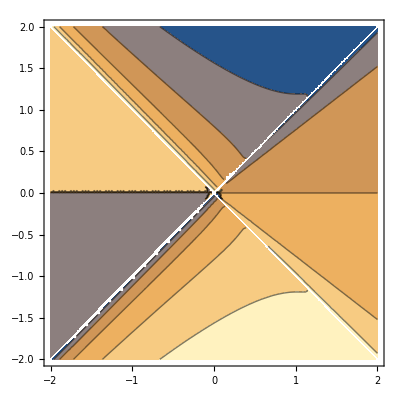

```mathematica
Ψ[κ_,t_,x_]=Piecewise[{{1/(π √2)ⅇ^((π κ)/(2a)-ⅈ κ/(2a)Log[(t+x)/(-(t-x))])BesselK[(ⅈ κ)/a,m √(-(t-x)(t+x))], t-x<0&&t+x>0}, {-ⅈ/2^(3/2)ⅇ^((π κ)/(2a)-ⅈ κ/(2a)Log[(t+x)/(t-x)])HankelH2[(ⅈ κ)/a,m √((t-x)(t+x))], t-x>0&&t+x>0}, {1/(π √2)ⅇ^(-(π κ)/(2a)-ⅈ κ/(2a)Log[(-(t+x))/(+(t-x))])BesselK[(ⅈ κ)/a,m √(-(t-x)(t+x))], t-x>0&&t+x<0}, {ⅈ/2^(3/2)ⅇ^(-(π κ)/(2a)-ⅈ κ/(2a)Log[(-(t+x))/(-(t-x))])HankelH1[(ⅈ κ)/a,m √((t-x)(t+x))], t-x<0&&t+x<0}, {0, True}}]
Ψ[κ,t,x]/.{a->1,κ->1,m->1}
(*ContourPlot[#[%],{x,-2,2},{t,-2,2}]&/@{Re,Im}
ContourPlot[#[%%],{x,-2,2},{t,-2,2}]&/@{Abs,Arg}*)
Simplify[ComplexExpand[1/(√(2Sinh[(π κ)/a]))(ⅇ^(+(π κ)/(2a))Ψ[κ,t,x]-ⅇ^(-(π κ)/(2a))Ψ[-κ,t,x]*)],Assumptions->κ>0&&a>0]
%/.{a->1,κ->1,m->1}
ContourPlot[#[%],{x,-2,2},{t,-2,2}]&/@{Re,Im}
ContourPlot[#[%%],{x,-2,2},{t,-2,2}]&/@{Abs,Arg}
```